## solution data

```mathematica
M3 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/heated_cavity/result_M3.txt","Table"];
```

```mathematica
M13 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/heated_cavity/result_M13.txt","Table"];
```

```mathematica
dvmSol = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/DVM/heated_cavity/result_DVM_10.txt","Table"];
```

```mathematica
GetQ[data_]:=Module[{qx,qy},

qx = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-2,ii⟧},{ii,1,Length[data⟦1⟧]}];
qy = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-1,ii⟧},{ii,1,Length[data⟦1⟧]}];

qx = Interpolation[qx];
qy = Interpolation[qy];

{qx,qy}
]
```

```mathematica
GetTheta[data_]:=Module[{theta},

theta = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦6,ii⟧},{ii,1,Length[data⟦1⟧]}];

theta = Interpolation[theta];

theta
]
```

## Plot heat streamlines

```mathematica
CompareStreamLines[momSol_,dvmSol_,Mvalue_]:=Module[{},

StreamPlot[{{momSol⟦1⟧[x,y],momSol⟦2⟧[x,y]},{dvmSol⟦1⟧[x,y],dvmSol⟦2⟧[x,y]}},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.1},ImageSize->Large,StreamStyle->{Red,Blue},PlotLegends->{Style[StringJoin["M=",ToString[Mvalue]],FontSize->14],Style["DVM",FontSize->14]},Frame->True,FrameTicksStyle->16]

]
```

```mathematica
qM3 = GetQ[M3];
qM13 = GetQ[M13];
qDVM = GetQ[dvmSol];
```

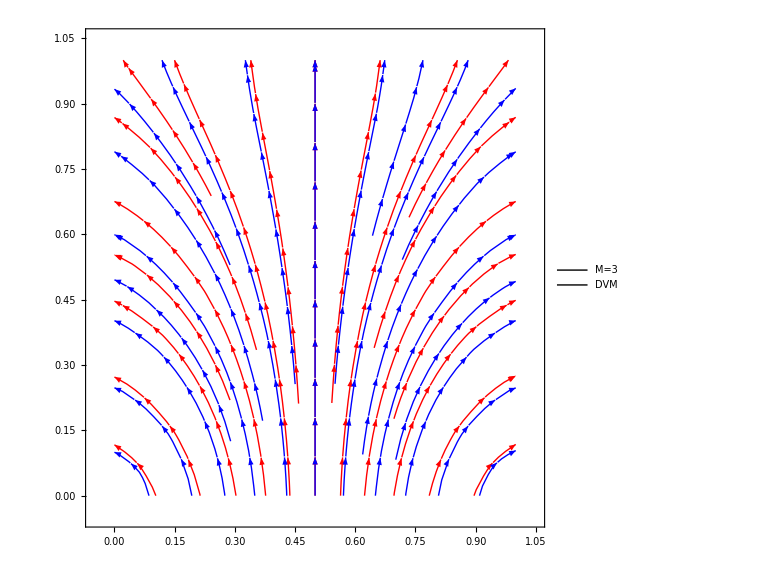

```mathematica
CompareStreamLines[qM3,qDVM,3]
```

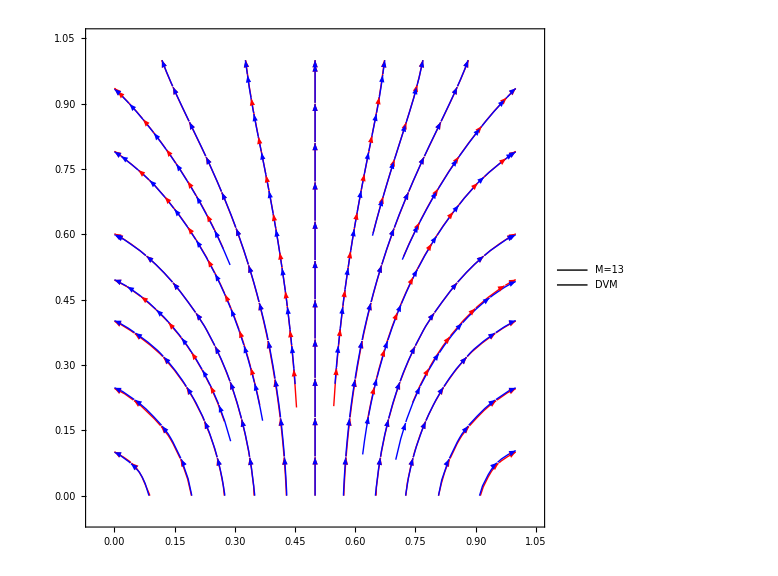

```mathematica
CompareStreamLines[qM13,qDVM,13]
```

## Plot contour theta

### plot contours

```mathematica
CompareThetaContours[dvmSol_,momSol_,Mvalue_]:=Module[{plotDVM,plotMom},

plotDVM = ContourPlot[dvmSol[x,y],{x,0,1},{y,0,1},ContourShading->None,ContourLabels->True,ContourStyle->Directive[Blue,Thick],Frame->True,FrameTicksStyle->Directive[Black,16],ImageSize->600,BaseStyle->{FontSize->15},FrameLabel->{{"y",None},{"x",None}},RotateLabel->False];

plotMom = ContourPlot[momSol[x,y],{x,0,1},{y,0,1},Frame->True,FrameTicksStyle->Directive[Black,16],ImageSize->600,BaseStyle->{FontSize->20},ContourStyle->Directive[Red,Thick],ContourShading->None,FrameLabel->{{"y",None},{"x",None}},RotateLabel->False];

Show[{plotMom,plotDVM}]

]
```

### Results

```mathematica
ThetaM3 = GetTheta[M3];
ThetaM13 = GetTheta[M13];
ThetaDVM = GetTheta[dvmSol];
```

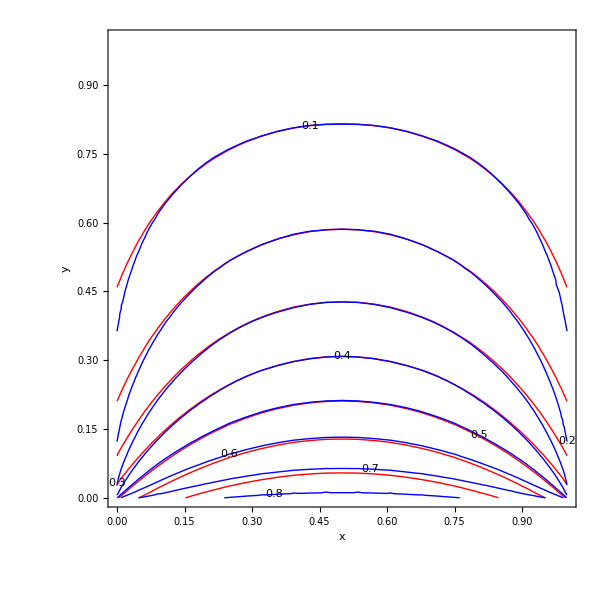

```mathematica
CompareThetaContours[ThetaDVM,ThetaM3,3]
```

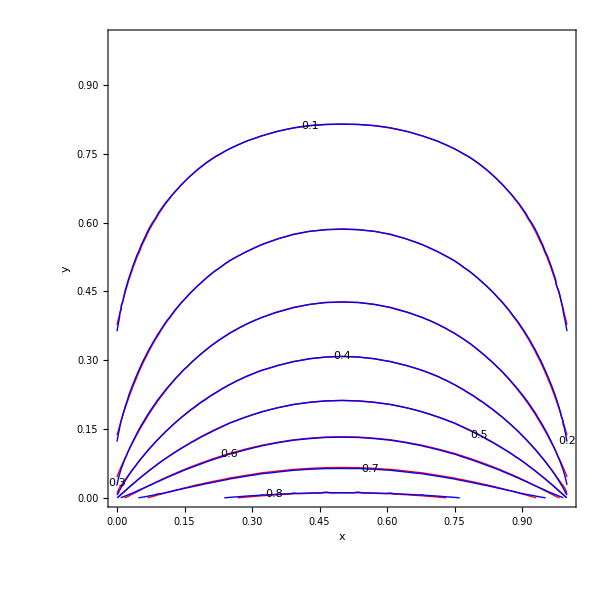

```mathematica
CompareThetaContours[ThetaDVM,ThetaM13,13]
```